Run admin, set real-time priority , unlimit CPU/GPU usage (if there is a limit set)
collect system info

1. CPU rendering 
 	generate a pic, parallel, time  ----multithreading performance
	somehow find single core performance too 
	calculation: find prime number
	test: integer, floating and string 
	do concurrency for every test set (or not) 
	
2. GPU rendering 
	render a pic, multi GPU I just assume Nvidia did their job so it will auto parallel it (I don’t have multi-GPU right now either), plus that programming the SLI / multiGPU capability could be another whole project
	calculation: find prime number 

3. RAM testing, not necessary performance since it will reflect on CPU performance most likely (Ryzen for example)
	single/multi core bandwidth and latency
	(not exactly sure how but this is normally how people test it)
	
	Actually, I found RAM testing is more complicated than I thought, so might just check how much RAM does the user have while 8G is decent, 16G is good, 32GB is super good...etc since RAM speed is not usually the reason that cause not smooth experience, the amount of RAM is. 
	Plus, I assume is harder to find a RAM that has an issue to test on than a normal one in summer school.
	

4. Disk-

	sequential read/write, random read/write (this is more important)
	don’t know if finding IOPS is possible on WL
	 output a 1 GB ish image or text file to boot drive, calculate time , delete afterwards, could output the image rendered by CPU 
	 
	 
	 
	 
In the end I will give each aspect a multiple number and have a total score at the end 
something like, CPUx10, GPUx9, DISKx3....etc.

run on few machines and rank them
too bad we don’t have powerful desktop here so can’t really set a limit for “super good”, but I think my laptop is decently good just don’t know when comparing to a desktop
but that’s the most easy part.

```mathematica
AbsoluteTiming[]
```

```mathematica
RepeatingElement[]
```

RepeatingElement[]

```mathematica
randText=Table[RandomString[],100]
```

```mathematica
WriteString[#, tempfile]& /@ randText //AbsoluteTiming
```

```mathematica
ClearAll[c]
```

```mathematica
ReadList[tempfile,String]//RepeatedTiming
```

```mathematica
ClearAll[
```

```mathematica
in=Table[MemoryInUse[],1000];
```

```mathematica
out=Table[MemoryInUse[],1000];
```

```mathematica
out2=Table[MemoryInUse[],1000];
```

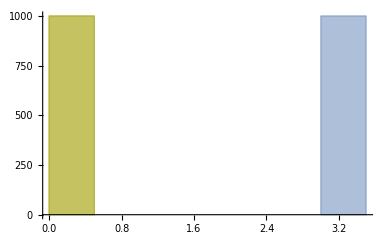

```mathematica
Histogram[{in,out,out2}]
```

```mathematica
ClearAll[c]
```

```mathematica
c=ConstantArray[0.,{1000,1000}];//RepeatedTiming
```

{0.0035,Null}

```mathematica
c=ConstantArray[0.,{10000,10000}];//RepeatedTiming
```

{0.34,Null}

```mathematica
c=ConstantArray[0.,{20000,20000}];//RepeatedTiming
```

{1.68,Null}

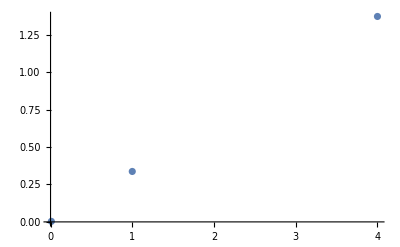

```mathematica
ListPlot[{{1000*1000,0.0035113120689655177`2.},{10000*10000,0.3368623749999999917`2.},{20000*20000,1.3719626499999999503`2.}}]
```

```mathematica
1/Quantity[1.3719626499999999503`2./(20000*20000)/64,"Seconds"/"Bytes"]
```

1.9×10^10 B/s

```mathematica
MemoryAvailable[]
```

6095585280

```mathematica
Map[Association,Association[SystemInformation[][[1]]]]["Devices"]["GraphicsDevices"]
```

{DirectX→{Version→9,Driver→igdumdim64.dll,Description→Intel(R) UHD Graphics 630,DeviceName→\\.\DISPLAY1,VendorId→32902,DeviceId→16027,SubSysId→537205336,Revision→0,DeviceIdentifier→{D7B78E66-7DDB-11CF-3160-6100BBC2D435},DriverVersion→25.20.100.6617,Optimized 3D Transparency→True},OpenGL→{OnScreen→{Vendor→Intel,Renderer→Intel(R) UHD Graphics 630,Version→4.5.0 - Build 25.20.100.6617,Extensions→{GL_3DFX_texture_compression_FXT1,GL_AMD_depth_clamp_separate,GL_AMD_vertex_shader_layer,GL_AMD_vertex_shader_viewport_index,GL_ARB_ES2_compatibility,GL_ARB_ES3_1_compatibility,GL_ARB_ES3_compatibility,GL_ARB_arrays_of_arrays,GL_ARB_base_instance,GL_ARB_bindless_texture,GL_ARB_blend_func_extended,GL_ARB_buffer_storage,GL_ARB_cl_event,GL_ARB_clear_buffer_object,GL_ARB_clear_texture,GL_ARB_clip_control,GL_ARB_color_buffer_float,GL_ARB_compatibility,GL_ARB_compressed_texture_pixel_storage,GL_ARB_compute_shader,GL_ARB_conditional_render_inverted,GL_ARB_conservative_depth,GL_ARB_copy_buffer,GL_ARB_copy_image,GL_ARB_cull_distance,GL_ARB_debug_output,GL_ARB_depth_buffer_float,GL_ARB_depth_clamp,GL_ARB_depth_texture,GL_ARB_derivative_control,GL_ARB_direct_state_access,GL_ARB_draw_buffers,GL_ARB_draw_buffers_blend,GL_ARB_draw_elements_base_vertex,GL_ARB_draw_indirect,GL_ARB_draw_instanced,GL_ARB_enhanced_layouts,GL_ARB_explicit_attrib_location,GL_ARB_explicit_uniform_location,GL_ARB_fragment_coord_conventions,GL_ARB_fragment_layer_viewport,GL_ARB_fragment_program,GL_ARB_fragment_program_shadow,GL_ARB_fragment_shader,GL_ARB_fragment_shader_interlock,GL_ARB_framebuffer_no_attachments,GL_ARB_framebuffer_object,GL_ARB_framebuffer_sRGB,GL_ARB_geometry_shader4,GL_ARB_get_program_binary,GL_ARB_get_texture_sub_image,GL_ARB_gl_spirv,GL_ARB_gpu_shader5,GL_ARB_gpu_shader_fp64,GL_ARB_half_float_pixel,GL_ARB_half_float_vertex,GL_ARB_indirect_parameters,GL_ARB_instanced_arrays,GL_ARB_internalformat_query,GL_ARB_internalformat_query2,GL_ARB_invalidate_subdata,GL_ARB_map_buffer_alignment,GL_ARB_map_buffer_range,GL_ARB_multi_bind,GL_ARB_multi_draw_indirect,GL_ARB_multisample,GL_ARB_multitexture,GL_ARB_occlusion_query,GL_ARB_occlusion_query2,GL_ARB_pipeline_statistics_query,GL_ARB_pixel_buffer_object,GL_ARB_point_parameters,GL_ARB_point_sprite,GL_ARB_polygon_offset_clamp,GL_ARB_post_depth_coverage,GL_ARB_program_interface_query,GL_ARB_provoking_vertex,GL_ARB_query_buffer_object,GL_ARB_robust_buffer_access_behavior,GL_ARB_robustness,GL_ARB_robustness_isolation,GL_ARB_sample_shading,GL_ARB_sampler_objects,GL_ARB_seamless_cube_map,GL_ARB_seamless_cubemap_per_texture,GL_ARB_separate_shader_objects,GL_ARB_shader_atomic_counter_ops,GL_ARB_shader_atomic_counters,GL_ARB_shader_bit_encoding,GL_ARB_shader_draw_parameters,GL_ARB_shader_group_vote,GL_ARB_shader_image_load_store,GL_ARB_shader_image_size,GL_ARB_shader_objects,GL_ARB_shader_precision,GL_ARB_shader_stencil_export,GL_ARB_shader_storage_buffer_object,GL_ARB_shader_subroutine,GL_ARB_shader_texture_image_samples,GL_ARB_shading_language_100,GL_ARB_shading_language_420pack,GL_ARB_shading_language_packing,GL_ARB_shadow,GL_ARB_spirv_extensions,GL_ARB_stencil_texturing,GL_ARB_sync,GL_ARB_tessellation_shader,GL_ARB_texture_barrier,GL_ARB_texture_border_clamp,GL_ARB_texture_buffer_object,GL_ARB_texture_buffer_object_rgb32,GL_ARB_texture_buffer_range,GL_ARB_texture_compression,GL_ARB_texture_compression_bptc,GL_ARB_texture_compression_rgtc,GL_ARB_texture_cube_map,GL_ARB_texture_cube_map_array,GL_ARB_texture_env_add,GL_ARB_texture_env_combine,GL_ARB_texture_env_crossbar,GL_ARB_texture_env_dot3,GL_ARB_texture_filter_anisotropic,GL_ARB_texture_float,GL_ARB_texture_gather,GL_ARB_texture_mirror_clamp_to_edge,GL_ARB_texture_mirrored_repeat,GL_ARB_texture_multisample,GL_ARB_texture_non_power_of_two,GL_ARB_texture_query_levels,GL_ARB_texture_query_lod,GL_ARB_texture_rectangle,GL_ARB_texture_rg,GL_ARB_texture_rgb10_a2ui,GL_ARB_texture_stencil8,GL_ARB_texture_storage,GL_ARB_texture_storage_multisample,GL_ARB_texture_swizzle,GL_ARB_texture_view,GL_ARB_timer_query,GL_ARB_transform_feedback2,GL_ARB_transform_feedback3,GL_ARB_transform_feedback_instanced,GL_ARB_transform_feedback_overflow_query,GL_ARB_transpose_matrix,GL_ARB_uniform_buffer_object,GL_ARB_vertex_array_bgra,GL_ARB_vertex_array_object,GL_ARB_vertex_attrib_64bit,GL_ARB_vertex_attrib_binding,GL_ARB_vertex_buffer_object,GL_ARB_vertex_program,GL_ARB_vertex_shader,GL_ARB_vertex_type_10f_11f_11f_rev,GL_ARB_vertex_type_2_10_10_10_rev,GL_ARB_viewport_array,GL_ARB_window_pos,GL_ATI_separate_stencil,GL_EXT_abgr,GL_EXT_bgra,GL_EXT_blend_color,GL_EXT_blend_equation_separate,GL_EXT_blend_func_separate,GL_EXT_blend_minmax,GL_EXT_blend_subtract,GL_EXT_clip_volume_hint,GL_EXT_compiled_vertex_array,GL_EXT_direct_state_access,GL_EXT_draw_buffers2,GL_EXT_draw_range_elements,GL_EXT_fog_coord,GL_EXT_framebuffer_blit,GL_EXT_framebuffer_multisample,GL_EXT_framebuffer_object,GL_EXT_geometry_shader4,GL_EXT_gpu_program_parameters,GL_EXT_gpu_shader4,GL_EXT_multi_draw_arrays,GL_EXT_packed_depth_stencil,GL_EXT_packed_float,GL_EXT_packed_pixels,GL_EXT_polygon_offset_clamp,GL_EXT_rescale_normal,GL_EXT_secondary_color,GL_EXT_separate_specular_color,GL_EXT_shader_framebuffer_fetch,GL_EXT_shader_integer_mix,GL_EXT_shadow_funcs,GL_EXT_stencil_two_side,GL_EXT_stencil_wrap,GL_EXT_texture3D,GL_EXT_texture_array,GL_EXT_texture_compression_s3tc,GL_EXT_texture_edge_clamp,GL_EXT_texture_env_add,GL_EXT_texture_env_combine,GL_EXT_texture_filter_anisotropic,GL_EXT_texture_integer,GL_EXT_texture_lod_bias,GL_EXT_texture_rectangle,GL_EXT_texture_sRGB,GL_EXT_texture_sRGB_decode,GL_EXT_texture_shared_exponent,GL_EXT_texture_snorm,GL_EXT_texture_storage,GL_EXT_texture_swizzle,GL_EXT_timer_query,GL_EXT_transform_feedback,GL_IBM_texture_mirrored_repeat,GL_INTEL_conservative_rasterization,GL_INTEL_fragment_shader_ordering,GL_INTEL_framebuffer_CMAA,GL_INTEL_map_texture,GL_INTEL_multi_rate_fragment_shader,GL_INTEL_performance_query,GL_KHR_blend_equation_advanced,GL_KHR_blend_equation_advanced_coherent,GL_KHR_context_flush_control,GL_KHR_debug,GL_KHR_no_error,GL_KHR_texture_compression_astc_hdr,GL_KHR_texture_compression_astc_ldr,GL_NV_blend_square,GL_NV_conditional_render,GL_NV_primitive_restart,GL_NV_texgen_reflection,GL_SGIS_generate_mipmap,GL_SGIS_texture_edge_clamp,GL_SGIS_texture_lod,GL_SUN_multi_draw_arrays,GL_WIN_swap_hint,WGL_EXT_swap_control},Optimized 3D Transparency→True,Max Samples→16},OffScreen→{Vendor→Intel,Renderer→Intel(R) UHD Graphics 630,Version→4.5.0 - Build 25.20.100.6617,Extensions→{GL_3DFX_texture_compression_FXT1,GL_AMD_depth_clamp_separate,GL_AMD_vertex_shader_layer,GL_AMD_vertex_shader_viewport_index,GL_ARB_ES2_compatibility,GL_ARB_ES3_1_compatibility,GL_ARB_ES3_compatibility,GL_ARB_arrays_of_arrays,GL_ARB_base_instance,GL_ARB_bindless_texture,GL_ARB_blend_func_extended,GL_ARB_buffer_storage,GL_ARB_cl_event,GL_ARB_clear_buffer_object,GL_ARB_clear_texture,GL_ARB_clip_control,GL_ARB_color_buffer_float,GL_ARB_compatibility,GL_ARB_compressed_texture_pixel_storage,GL_ARB_compute_shader,GL_ARB_conditional_render_inverted,GL_ARB_conservative_depth,GL_ARB_copy_buffer,GL_ARB_copy_image,GL_ARB_cull_distance,GL_ARB_debug_output,GL_ARB_depth_buffer_float,GL_ARB_depth_clamp,GL_ARB_depth_texture,GL_ARB_derivative_control,GL_ARB_direct_state_access,GL_ARB_draw_buffers,GL_ARB_draw_buffers_blend,GL_ARB_draw_elements_base_vertex,GL_ARB_draw_indirect,GL_ARB_draw_instanced,GL_ARB_enhanced_layouts,GL_ARB_explicit_attrib_location,GL_ARB_explicit_uniform_location,GL_ARB_fragment_coord_conventions,GL_ARB_fragment_layer_viewport,GL_ARB_fragment_program,GL_ARB_fragment_program_shadow,GL_ARB_fragment_shader,GL_ARB_fragment_shader_interlock,GL_ARB_framebuffer_no_attachments,GL_ARB_framebuffer_object,GL_ARB_framebuffer_sRGB,GL_ARB_geometry_shader4,GL_ARB_get_program_binary,GL_ARB_get_texture_sub_image,GL_ARB_gl_spirv,GL_ARB_gpu_shader5,GL_ARB_gpu_shader_fp64,GL_ARB_half_float_pixel,GL_ARB_half_float_vertex,GL_ARB_indirect_parameters,GL_ARB_instanced_arrays,GL_ARB_internalformat_query,GL_ARB_internalformat_query2,GL_ARB_invalidate_subdata,GL_ARB_map_buffer_alignment,GL_ARB_map_buffer_range,GL_ARB_multi_bind,GL_ARB_multi_draw_indirect,GL_ARB_multisample,GL_ARB_multitexture,GL_ARB_occlusion_query,GL_ARB_occlusion_query2,GL_ARB_pipeline_statistics_query,GL_ARB_pixel_buffer_object,GL_ARB_point_parameters,GL_ARB_point_sprite,GL_ARB_polygon_offset_clamp,GL_ARB_post_depth_coverage,GL_ARB_program_interface_query,GL_ARB_provoking_vertex,GL_ARB_query_buffer_object,GL_ARB_robust_buffer_access_behavior,GL_ARB_robustness,GL_ARB_robustness_isolation,GL_ARB_sample_shading,GL_ARB_sampler_objects,GL_ARB_seamless_cube_map,GL_ARB_seamless_cubemap_per_texture,GL_ARB_separate_shader_objects,GL_ARB_shader_atomic_counter_ops,GL_ARB_shader_atomic_counters,GL_ARB_shader_bit_encoding,GL_ARB_shader_draw_parameters,GL_ARB_shader_group_vote,GL_ARB_shader_image_load_store,GL_ARB_shader_image_size,GL_ARB_shader_objects,GL_ARB_shader_precision,GL_ARB_shader_stencil_export,GL_ARB_shader_storage_buffer_object,GL_ARB_shader_subroutine,GL_ARB_shader_texture_image_samples,GL_ARB_shading_language_100,GL_ARB_shading_language_420pack,GL_ARB_shading_language_packing,GL_ARB_shadow,GL_ARB_spirv_extensions,GL_ARB_stencil_texturing,GL_ARB_sync,GL_ARB_tessellation_shader,GL_ARB_texture_barrier,GL_ARB_texture_border_clamp,GL_ARB_texture_buffer_object,GL_ARB_texture_buffer_object_rgb32,GL_ARB_texture_buffer_range,GL_ARB_texture_compression,GL_ARB_texture_compression_bptc,GL_ARB_texture_compression_rgtc,GL_ARB_texture_cube_map,GL_ARB_texture_cube_map_array,GL_ARB_texture_env_add,GL_ARB_texture_env_combine,GL_ARB_texture_env_crossbar,GL_ARB_texture_env_dot3,GL_ARB_texture_filter_anisotropic,GL_ARB_texture_float,GL_ARB_texture_gather,GL_ARB_texture_mirror_clamp_to_edge,GL_ARB_texture_mirrored_repeat,GL_ARB_texture_multisample,GL_ARB_texture_non_power_of_two,GL_ARB_texture_query_levels,GL_ARB_texture_query_lod,GL_ARB_texture_rectangle,GL_ARB_texture_rg,GL_ARB_texture_rgb10_a2ui,GL_ARB_texture_stencil8,GL_ARB_texture_storage,GL_ARB_texture_storage_multisample,GL_ARB_texture_swizzle,GL_ARB_texture_view,GL_ARB_timer_query,GL_ARB_transform_feedback2,GL_ARB_transform_feedback3,GL_ARB_transform_feedback_instanced,GL_ARB_transform_feedback_overflow_query,GL_ARB_transpose_matrix,GL_ARB_uniform_buffer_object,GL_ARB_vertex_array_bgra,GL_ARB_vertex_array_object,GL_ARB_vertex_attrib_64bit,GL_ARB_vertex_attrib_binding,GL_ARB_vertex_buffer_object,GL_ARB_vertex_program,GL_ARB_vertex_shader,GL_ARB_vertex_type_10f_11f_11f_rev,GL_ARB_vertex_type_2_10_10_10_rev,GL_ARB_viewport_array,GL_ARB_window_pos,GL_ATI_separate_stencil,GL_EXT_abgr,GL_EXT_bgra,GL_EXT_blend_color,GL_EXT_blend_equation_separate,GL_EXT_blend_func_separate,GL_EXT_blend_minmax,GL_EXT_blend_subtract,GL_EXT_clip_volume_hint,GL_EXT_compiled_vertex_array,GL_EXT_direct_state_access,GL_EXT_draw_buffers2,GL_EXT_draw_range_elements,GL_EXT_fog_coord,GL_EXT_framebuffer_blit,GL_EXT_framebuffer_multisample,GL_EXT_framebuffer_object,GL_EXT_geometry_shader4,GL_EXT_gpu_program_parameters,GL_EXT_gpu_shader4,GL_EXT_multi_draw_arrays,GL_EXT_packed_depth_stencil,GL_EXT_packed_float,GL_EXT_packed_pixels,GL_EXT_polygon_offset_clamp,GL_EXT_rescale_normal,GL_EXT_secondary_color,GL_EXT_separate_specular_color,GL_EXT_shader_framebuffer_fetch,GL_EXT_shader_integer_mix,GL_EXT_shadow_funcs,GL_EXT_stencil_two_side,GL_EXT_stencil_wrap,GL_EXT_texture3D,GL_EXT_texture_array,GL_EXT_texture_compression_s3tc,GL_EXT_texture_edge_clamp,GL_EXT_texture_env_add,GL_EXT_texture_env_combine,GL_EXT_texture_filter_anisotropic,GL_EXT_texture_integer,GL_EXT_texture_lod_bias,GL_EXT_texture_rectangle,GL_EXT_texture_sRGB,GL_EXT_texture_sRGB_decode,GL_EXT_texture_shared_exponent,GL_EXT_texture_snorm,GL_EXT_texture_storage,GL_EXT_texture_swizzle,GL_EXT_timer_query,GL_EXT_transform_feedback,GL_IBM_texture_mirrored_repeat,GL_INTEL_conservative_rasterization,GL_INTEL_fragment_shader_ordering,GL_INTEL_framebuffer_CMAA,GL_INTEL_map_texture,GL_INTEL_multi_rate_fragment_shader,GL_INTEL_performance_query,GL_KHR_blend_equation_advanced,GL_KHR_blend_equation_advanced_coherent,GL_KHR_context_flush_control,GL_KHR_debug,GL_KHR_no_error,GL_KHR_texture_compression_astc_hdr,GL_KHR_texture_compression_astc_ldr,GL_NV_blend_square,GL_NV_conditional_render,GL_NV_primitive_restart,GL_NV_texgen_reflection,GL_SGIS_generate_mipmap,GL_SGIS_texture_edge_clamp,GL_SGIS_texture_lod,GL_SUN_multi_draw_arrays,GL_WIN_swap_hint,WGL_EXT_swap_control},Optimized 3D Transparency→True,Max Samples→16}},Mesa→{Vendor→VMware, Inc.,Renderer→Gallium 0.4 on llvmpipe (LLVM 3.6, 256 bits),Version→3.0 Mesa 10.6.8 (git-fbfd450),Extensions→{GL_ARB_multisample,GL_EXT_abgr,GL_EXT_bgra,GL_EXT_blend_color,GL_EXT_blend_minmax,GL_EXT_blend_subtract,GL_EXT_copy_texture,GL_EXT_polygon_offset,GL_EXT_subtexture,GL_EXT_texture_object,GL_EXT_vertex_array,GL_EXT_compiled_vertex_array,GL_EXT_texture,GL_EXT_texture3D,GL_IBM_rasterpos_clip,GL_ARB_point_parameters,GL_EXT_draw_range_elements,GL_EXT_packed_pixels,GL_EXT_point_parameters,GL_EXT_rescale_normal,GL_EXT_separate_specular_color,GL_EXT_texture_edge_clamp,GL_SGIS_generate_mipmap,GL_SGIS_texture_border_clamp,GL_SGIS_texture_edge_clamp,GL_SGIS_texture_lod,GL_ARB_framebuffer_sRGB,GL_ARB_multitexture,GL_EXT_framebuffer_sRGB,GL_IBM_multimode_draw_arrays,GL_IBM_texture_mirrored_repeat,GL_ARB_texture_cube_map,GL_ARB_texture_env_add,GL_ARB_transpose_matrix,GL_EXT_blend_func_separate,GL_EXT_fog_coord,GL_EXT_multi_draw_arrays,GL_EXT_secondary_color,GL_EXT_texture_env_add,GL_EXT_texture_lod_bias,GL_INGR_blend_func_separate,GL_NV_blend_square,GL_NV_light_max_exponent,GL_NV_texgen_reflection,GL_NV_texture_env_combine4,GL_SUN_multi_draw_arrays,GL_ARB_texture_border_clamp,GL_ARB_texture_compression,GL_EXT_framebuffer_object,GL_EXT_texture_env_combine,GL_EXT_texture_env_dot3,GL_MESA_window_pos,GL_NV_packed_depth_stencil,GL_NV_texture_rectangle,GL_ARB_depth_texture,GL_ARB_occlusion_query,GL_ARB_shadow,GL_ARB_texture_env_combine,GL_ARB_texture_env_crossbar,GL_ARB_texture_env_dot3,GL_ARB_texture_mirrored_repeat,GL_ARB_window_pos,GL_EXT_stencil_two_side,GL_EXT_texture_cube_map,GL_NV_depth_clamp,GL_NV_fog_distance,GL_APPLE_packed_pixels,GL_APPLE_vertex_array_object,GL_ARB_draw_buffers,GL_ARB_fragment_program,GL_ARB_fragment_shader,GL_ARB_shader_objects,GL_ARB_vertex_program,GL_ARB_vertex_shader,GL_ATI_draw_buffers,GL_ATI_texture_env_combine3,GL_ATI_texture_float,GL_EXT_shadow_funcs,GL_EXT_stencil_wrap,GL_MESA_pack_invert,GL_MESA_ycbcr_texture,GL_NV_primitive_restart,GL_ARB_depth_clamp,GL_ARB_fragment_program_shadow,GL_ARB_half_float_pixel,GL_ARB_occlusion_query2,GL_ARB_point_sprite,GL_ARB_shading_language_100,GL_ARB_sync,GL_ARB_texture_non_power_of_two,GL_ARB_vertex_buffer_object,GL_ATI_blend_equation_separate,GL_EXT_blend_equation_separate,GL_OES_read_format,GL_ARB_color_buffer_float,GL_ARB_pixel_buffer_object,GL_ARB_texture_compression_rgtc,GL_ARB_texture_float,GL_ARB_texture_rectangle,GL_ATI_texture_compression_3dc,GL_EXT_packed_float,GL_EXT_pixel_buffer_object,GL_EXT_texture_compression_rgtc,GL_EXT_texture_mirror_clamp,GL_EXT_texture_rectangle,GL_EXT_texture_sRGB,GL_EXT_texture_shared_exponent,GL_ARB_framebuffer_object,GL_EXT_framebuffer_blit,GL_EXT_framebuffer_multisample,GL_EXT_packed_depth_stencil,GL_ARB_vertex_array_object,GL_ATI_separate_stencil,GL_ATI_texture_mirror_once,GL_EXT_draw_buffers2,GL_EXT_draw_instanced,GL_EXT_gpu_program_parameters,GL_EXT_texture_array,GL_EXT_texture_compression_latc,GL_EXT_texture_integer,GL_EXT_texture_sRGB_decode,GL_EXT_timer_query,GL_OES_EGL_image,GL_ARB_copy_buffer,GL_ARB_depth_buffer_float,GL_ARB_draw_instanced,GL_ARB_half_float_vertex,GL_ARB_instanced_arrays,GL_ARB_map_buffer_range,GL_ARB_texture_rg,GL_ARB_texture_swizzle,GL_ARB_vertex_array_bgra,GL_EXT_texture_swizzle,GL_EXT_vertex_array_bgra,GL_NV_conditional_render,GL_AMD_conservative_depth,GL_AMD_draw_buffers_blend,GL_AMD_seamless_cubemap_per_texture,GL_ARB_ES2_compatibility,GL_ARB_blend_func_extended,GL_ARB_debug_output,GL_ARB_draw_buffers_blend,GL_ARB_draw_elements_base_vertex,GL_ARB_explicit_attrib_location,GL_ARB_fragment_coord_conventions,GL_ARB_provoking_vertex,GL_ARB_sampler_objects,GL_ARB_seamless_cube_map,GL_ARB_shader_texture_lod,GL_ARB_texture_cube_map_array,GL_ARB_texture_gather,GL_ARB_texture_multisample,GL_ARB_texture_rgb10_a2ui,GL_ARB_uniform_buffer_object,GL_ARB_vertex_type_2_10_10_10_rev,GL_EXT_provoking_vertex,GL_EXT_texture_snorm,GL_MESA_texture_signed_rgba,GL_ARB_get_program_binary,GL_ARB_robustness,GL_ARB_separate_shader_objects,GL_ARB_shader_bit_encoding,GL_ARB_timer_query,GL_ARB_transform_feedback2,GL_ARB_transform_feedback3,GL_ARB_base_instance,GL_ARB_compressed_texture_pixel_storage,GL_ARB_conservative_depth,GL_ARB_internalformat_query,GL_ARB_map_buffer_alignment,GL_ARB_shading_language_420pack,GL_ARB_shading_language_packing,GL_ARB_texture_storage,GL_ARB_transform_feedback_instanced,GL_EXT_framebuffer_multisample_blit_scaled,GL_EXT_transform_feedback,GL_AMD_shader_trinary_minmax,GL_ARB_ES3_compatibility,GL_ARB_clear_buffer_object,GL_ARB_explicit_uniform_location,GL_ARB_invalidate_subdata,GL_ARB_program_interface_query,GL_ARB_stencil_texturing,GL_ARB_texture_query_levels,GL_ARB_texture_storage_multisample,GL_ARB_texture_view,GL_ARB_vertex_attrib_binding,GL_KHR_debug,GL_ARB_buffer_storage,GL_ARB_multi_bind,GL_ARB_seamless_cubemap_per_texture,GL_ARB_texture_mirror_clamp_to_edge,GL_ARB_texture_stencil8,GL_ARB_vertex_type_10f_11f_11f_rev,GL_EXT_shader_integer_mix,GL_ARB_clip_control,GL_ARB_conditional_render_inverted,GL_EXT_polygon_offset_clamp,GL_KHR_context_flush_control},Optimized 3D Transparency→True,Max Samples→0}}

```mathematica
SystemInformation[]
```

1234567

```mathematica
Needs["MXNetLink`"]
```

```mathematica
?*SMI*
```

```mathematica
MXNetLink`GetSMIToolInformation[]
```

{<|Name→GeForce RTX 2070 with Max-Q Design,TotalMemory→8192000000,FreeMemory→8031000000,Temperature→52,PowerUsage→29.47,Utilization→0|>}

```mathematica
Keys@Association[SystemInformation[][[1]]]
```

{Kernel,FrontEnd,Links,Parallel,Devices,Network,Machine}